```mathematica
f[x_]=r x(1-x)
soln = ParametricNDSolve[{x'[t]==f[x[t]],x[0]==x0},x,{t,0,20},{r,x0}]
```

r (1-x) x

{x→ParametricFunction[<>]}

InterpolatingFunction[…][t]

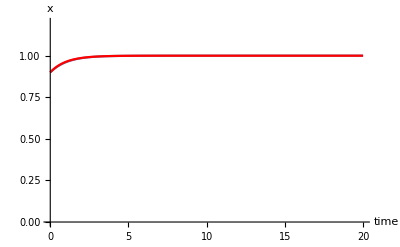

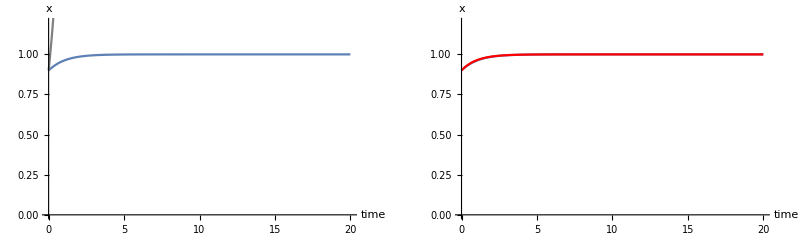

```mathematica
r0 = 1;
x00 = 0.9;
xfunc[t_]= x[r0,x00][t]/.soln
exact = Plot[xfunc[t],{t,0,20},AxesLabel->{"time","x"},PlotRange->{{0,20},{0,1.2}},LabelStyle->Medium];
approx1 = Plot[x00 Exp[r0 t],{t,0,20},PlotStyle->Gray];
approx2 = Plot[1+(x00-1 )Exp[-r0 t],{t,0,20},PlotStyle->Red,PlotRange->{{0,20},{0,1.2}}];
Show[exact, approx2]
GraphicsGrid[{{Show[exact,approx1],Show[exact, approx2]}}]
```